```mathematica
f1[x_,y_,z_]:=1-1/z;
f2[x_,y_,z_]:=1/(y-x);
x0=0;
y0=-1;
z0=1;
b=1;
```

Построим разбиение отрезка, на котором ищется решение данной задачи Коши

```mathematica
n=10;
h=(b-x0)/n;
X=Table[x0+(k-1)*h,{k,1,n+1}];
```

Реализуем алгоритм метода Эйлера для решения задачи Коши для системы дифференциальных уравнений

```mathematica
Y=Table[0,{k,1,n+1}];
Z=Table[0,{k,1,n+1}];
Y[[1]]=y0;
Z[[1]]=z0;
For[k=2,k≤n+1,k++,Y[[k]]=Y[[k-1]]+h*f1[X[[k-1]],Y[[k-1]],Z[[k-1]]];Z[[k]]=Z[[k-1]]+h*f2[X[[k-1]],Y[[k-1]],Z[[k-1]]]]
```

Выполним интерполяцию найденного приближенного решения задачи Коши для системы дифференциальных уравнений и построим его график

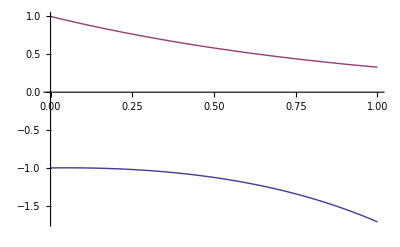

```mathematica
XY=Table[{X[[k]],Y[[k]]},{k,1,n+1}];
XZ=Table[{X[[k]],Z[[k]]},{k,1,n+1}];
y=Interpolation[XY];
z=Interpolation[XZ];
G=Plot[{y[x],z[x]},{x,x0,b}]
```